# Abundance Calculations

From EcoCyc:  monomer concentrations for MOPS medium with 2% glucose
From Bionumbers/Papers: volume of E. coli cell under MOPS medium

```mathematica
CalculateEnzymeConcentration[row_,Vcell_]:=(row[["GPCN"]]/(Vcell NA))/row[["MolPerComplex"]]
NA=6.02214076 10^23
Vcell={2.9 10^-15,3.0 10^-15,3.1 10^-15}
enzymes=Dataset[{
<|"Enzyme"->"FabA","GPCN"->4392,"MolPerComplex"->2|>,
<|"Enzyme"->"FabB","GPCN"->3376,"MolPerComplex"->2|>,
<|"Enzyme"->"FabD","GPCN"->3142,"MolPerComplex"->1|>,
<|"Enzyme"->"FabF","GPCN"->1598,"MolPerComplex"->2|>,
<|"Enzyme"->"FabG","GPCN"->4015,"MolPerComplex"->4|>,
<|"Enzyme"->"FabH","GPCN"->1564,"MolPerComplex"->2|>,
<|"Enzyme"->"FabI","GPCN"->8248,"MolPerComplex"->4|>,
<|"Enzyme"->"FabZ","GPCN"->3099,"MolPerComplex"->6|>,
<|"Enzyme"->"LpxA","GPCN"->754,"MolPerComplex"->3|>,
<|"Enzyme"->"LpxC","GPCN"->2844,"MolPerComplex"->1|>,
<|"Enzyme"->"LpxD","GPCN"->982,"MolPerComplex"->3|>,
<|"Enzyme"->"PlsB","GPCN"->445,"MolPerComplex"->1|>,
<|"Enzyme"->"PlsC","GPCN"->174,"MolPerComplex"->1|>,
<|"Enzyme"->"CdsA","GPCN"->182,"MolPerComplex"->1|>,
<|"Enzyme"->"ACP","GPCN"->85961,"MolPerComplex"->1|>}];
enzymeConcentrations=enzymes[
All,
Append[#,"Concentration"->CalculateEnzymeConcentration[#,Vcell]]&]
```

6.02214×10^23

{2.9×10^-15,3.×10^-15,3.1×10^-15}

Plot the concentrations of the enzymes

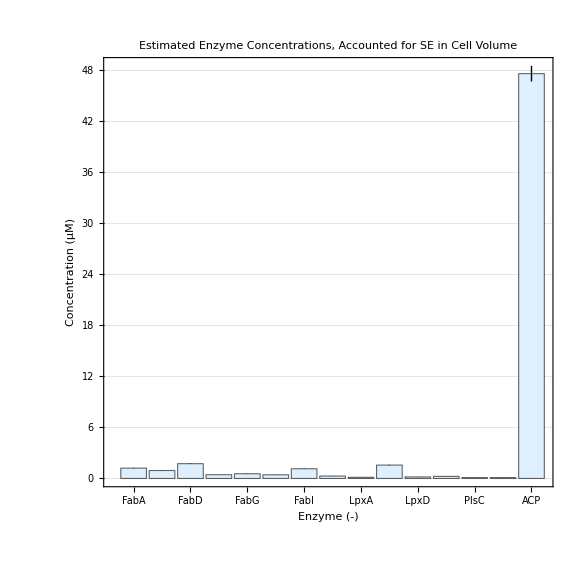

```mathematica
values=enzymeConcentrations[All,Around[Mean[#Concentration],StandardDeviation[#Concentration]/Sqrt[Length[#Concentration]]]&]//Normal;
labels=enzymeConcentrations[[All,"Enzyme"]]//Normal;
BarChart[values 10^6,ChartLabels->labels,Frame->True,FrameLabel->{"Enzyme (-)","Concentration (μM)"},ChartStyle->Directive[EdgeForm[Black], LightBlue],ImageSize->Large,GridLines->Automatic,PlotLabel->"Estimated Enzyme Concentrations, Accounted for SE in Cell Volume",AspectRatio->1]
```

Save the FAS enzyme estimates to a .csv

```mathematica
enzAssociations={"FabA"->e9tot,"FabB"->e10tot,"FabD"->e2tot,"FabF"->e8tot,"FabG"->e4tot,"FabH"->e3tot,"FabI"->e6tot,"FabZ"->e5tot};
exportList=Thread[{Normal[enzymeConcentrations[[;;8,"Enzyme"]]/.enzAssociations],10^6 Normal[enzymeConcentrations[[All,"Concentration"]][[;;8,2]]]}];
exportList=Join[exportList,{{e1tot,0},{e7tot,0}}]; (* These concentrations are for ACC and TesA respectively *)
Export[FileNameJoin[ParentDirectory[NotebookDirectory[]],"data/FAS","FAS_enzyme_concentrations.csv"],exportList,"CSV"]
```

/home/jacobr/Documents/Masters/Thesis/Project/phospholipid-synthesis-dynamics/model/data/FAS_enzyme_concentrations.csv